```mathematica
SetDirectory[NotebookDirectory[]];
```

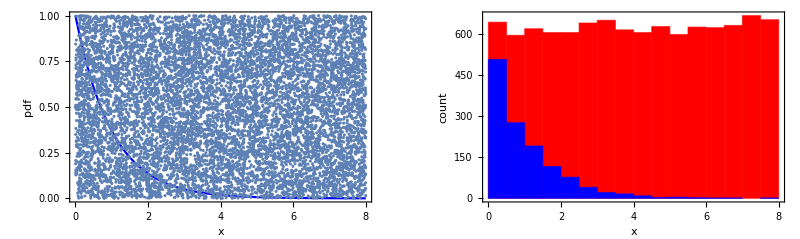

```mathematica
n = 10000;
x=RandomVariate[UniformDistribution[{0,8}],{n}];
y=RandomVariate[UniformDistribution[{0,1}],{n}];
g1=Show[Plot[PDF[ExponentialDistribution[1],x],{x,0,8},PlotRange->Full,PlotStyle->Blue,Frame->{True,True,False,False},FrameLabel->{"x","pdf"},BaseStyle->{FontSize->18}],(ListPlot[Thread[{x,y}],FrameLabel->{"",""},Frame->{False,False,False,False},Axes->{False,False,False,False},Joined->True,ColorFunction->Function[{x,y},If[y<Exp[-x],Blue,Red]],ColorFunctionScaling->False]/.Line[a__]:>Point[a])];
lCoords = Thread[{x,y}];
lXAccepted = If[#[[2]]<PDF[ExponentialDistribution[1],#[[1]]],#[[1]],-1]&/@lCoords;
lXAccepted=Cases[lXAccepted,_?NonNegative];
g2=Show[Histogram[x,20,ChartStyle->Red,Frame->{True,True,False,False},FrameLabel->{"x","count"}],Histogram[lXAccepted,20,ChartStyle->Blue]];
gFinal=Show[GraphicsRow[{g1,g2}],ImageSize->800]
```

```mathematica
Export["MCMC_rejectionSamplingExponential.pdf",gFinal]
```

MCMC_rejectionSamplingExponential.pdf